## 電球の抵抗

```mathematica
ClearAll["Global`*"]
```

### 抵抗器 （線形）

```mathematica
batteryNum={1,2,3,4,5};
Cteikou={0.1110,0.2105,0.326,0.424,0.502};
Vteikou={1.140,2.135,3.338,4.312,5.124};
Rteikou= Vteikou/Cteikou
Print["平均抵抗　",Mean[Rteikou]]
Grid[Join[{{"電池本数","電流","電圧","抵抗","抵抗誤差%"}},Transpose@{batteryNum,Cteikou,Vteikou,Rteikou,(Rteikou/Mean[Rteikou]-1)*100}],Frame->All]
(*テスターの結果を公称値とする．*)
Print["抵抗の平均値：",Mean[Rteikou]]
Print["公称値を10.2Ωとした場合の平均値の誤差：",Abs@(Mean[Rteikou]/10.2-1)*100]
Print["公称値を10.2Ωとした場合の平均値の誤差：",Mean[Abs@(Rteikou/10.2-1)*100]]
```

{10.2703,10.1425,10.2393,10.1698,10.2072}

平均抵抗　10.2058

電池本数 | 電流 | 電圧 | 抵抗 | 抵抗誤差%
1 | 0.111 | 1.14 | 10.2703 | 0.631634
2 | 0.2105 | 2.135 | 10.1425 | -0.620128
3 | 0.326 | 3.338 | 10.2393 | 0.327822
4 | 0.424 | 4.312 | 10.1698 | -0.352697
5 | 0.502 | 5.124 | 10.2072 | 0.013369

抵抗の平均値：10.2058

公称値を10.2Ωとした場合の平均値の誤差：0.0569304

公称値を10.2Ωとした場合の平均値の誤差：0.400738

### 豆電球 （非線形）

```mathematica
batteryNum={0,1,2,3,4,5};
Cmame={10^-10,0.1810,0.2755,0.338,0.392,0.464};
Vmame={1.3*10^-10,0.980,2.189,3.246,4.262,5.497};
Tmame={0,750,1000,1100,1200,1300};(*目分量*)
Wmame= Vmame*Cmame
Rmame= Vmame/Cmame
Mean[Rmame]
```

{1.3×10^-20,0.17738,0.60307,1.09715,1.6707,2.55061}

{1.3,5.41436,7.94555,9.60355,10.8724,11.847}

7.83048

```mathematica
Grid[Join[{{"電池本数","電流","電圧","抵抗","電力","おおよその温度"}},Transpose@{batteryNum,Cmame,Vmame,Rmame,Wmame,Tmame}],Frame->All]
```

電池本数 | 電流 | 電圧 | 抵抗 | 電力 | おおよその温度
0 | 1/10000000000 | 1.3×10^-10 | 1.3 | 1.3×10^-20 | 0
1 | 0.181 | 0.98 | 5.41436 | 0.17738 | 750
2 | 0.2755 | 2.189 | 7.94555 | 0.60307 | 1000
3 | 0.338 | 3.246 | 9.60355 | 1.09715 | 1100
4 | 0.392 | 4.262 | 10.8724 | 1.6707 | 1200
5 | 0.464 | 5.497 | 11.847 | 2.55061 | 1300

0.00101161+0.166233 x^0.5+0.0124581 x

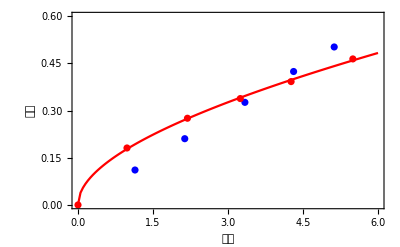

{{1.3×10^-20,1.3},{0.17738,5.41436},{0.60307,7.94555},{1.09715,9.60355},{1.6707,10.8724},{2.55061,11.847}}

{a→1.32925,b→-2.45645,c→10.5143,d→0.}

1.32925+10.5143 x^0.5-2.45645 x

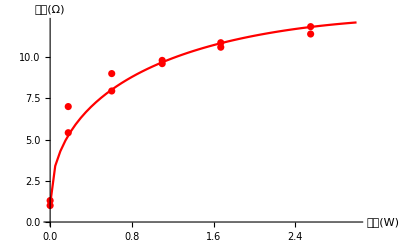

```mathematica
Fit[Transpose[{Vmame,Cmame}],{1,x,x^0.5},x]
CmameFit[x_]=0.0010118343854506999+0.1662327674314839 x^0.5+0.012458165242618707 x;
Show[
{ListPlot[Transpose[{Vteikou,Cteikou}],Joined->False,PlotStyle->Blue],
ListPlot[Transpose[{Vmame,Cmame}],Joined->False,PlotStyle->Red],
ListPlot[Table[{c,CmameFit[c]},{c,0,6,.05}],Joined->True,PlotStyle->Red]},
AxesLabel->{"電圧","電流"},
PlotRange->{{0,6},{0,0.6}},
Frame->True
]

Transpose[{Wmame,Rmame}]
(*ans=FindFit[%,a+b* x+c*x^2,{a,b,c,d},x]*)
ans=FindFit[%,a+b* x+c*x^0.5,{a,b,c,d},x]
(a+b* x+c*x^0.5)/.ans
RmameFit[x_]=1.0629004957413175+11.070851150612162 x^0.5-2.7121572307781956 x;
Show[
{ListPlot[Table[{w,RmameFit[w]},{w,0,3,.05}],
Joined->True,
PlotStyle->Red,
AxesLabel->{"電力(W)","抵抗(Ω)"}],
ListPlot[Transpose[{Wmame,Rmame}],Joined->False,PlotStyle->Red],
ListPlot[Transpose[{Wmame,1+0.008*Tmame}],Joined->False,PlotStyle->Red]
}
]
```

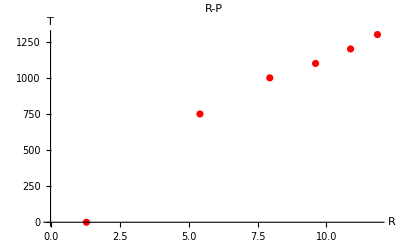

```mathematica
ListPlot[Transpose[{Rmame,Tmame}],Joined->False,PlotStyle->Red,PlotLabel->"R-P",AxesLabel->{"R","T"}]
```